```mathematica
data={{1,347},{2,264},{3,264},{4,308},{5,316},{6,264},{7,264},{8,376},{9,264},{10,264},{11,264},{12,470},{13,313},{14,264},{15,264},{16,316},{17,264},{18,264},{19,322},{20,264},{21,264},{22,264},{23,331},{24,264},{25,264},{26,264},{27,317},{28,264},{29,264},{30,264},{31,322},{32,264},{33,264},{34,363},{35,264},{36,264},{37,264},{38,387},{39,264},{40,264},{41,272},{42,342},{43,264},{44,264},{45,347},{46,264},{47,264},{48,264},{49,340},{50,264}};
lm=LinearModelFit[data,x,x];
```

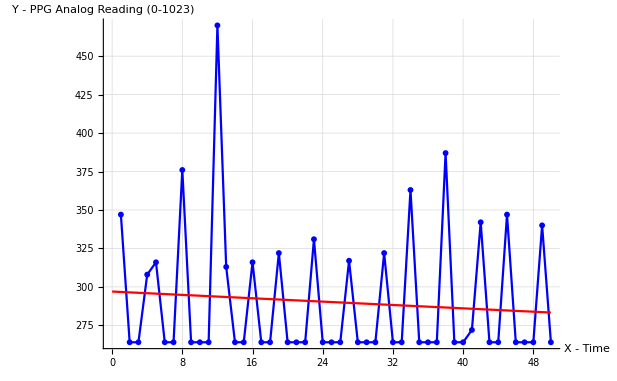

```mathematica
Show[ListLinePlot[data,PlotStyle->Blue,PlotMarkers->{Automatic, 6},GridLines->Automatic],Plot[lm[x],{x,0,50},PlotStyle->Red],AxesLabel->{"X - Time","Y - PPG Analog Reading (0-1023)"},PslotLabel->lm["BestFit"]]
```

```mathematica
data2={{1,265},{2,471},{3,264},{4,264},{5,574},{6,264},{7,264},{8,264},{9,640},{10,264},{11,264},{12,264},{13,558},{14,275},{15,264},{16,264},{17,440},{18,264},{19,264},{20,264},{21,450},{22,264},{23,265},{24,264},{25,466},{26,264},{27,264},{28,264},{29,487},{30,264},{31,264},{32,264},{33,476},{34,280},{35,264},{36,264},{37,446},{38,264},{39,264},{40,264},{41,338},{42,434},{43,265},{44,264},{45,303},{46,333},{47,264},{48,264},{49,307},{50,264}};
```

```mathematica
lm2=LinearModelFit[data2,x,x];
```

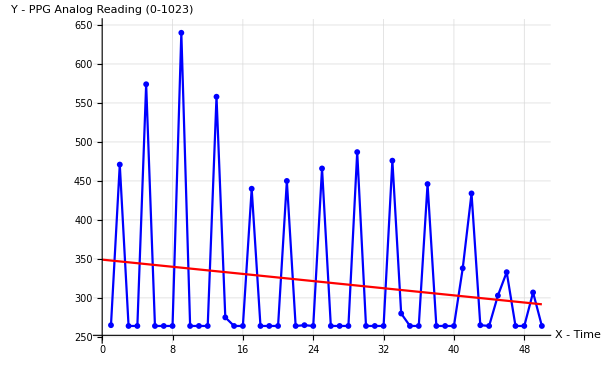

```mathematica
Show[ListLinePlot[data2,PlotStyle->Blue,PlotMarkers->{Automatic, 6},PlotRange->{250,650},GridLines->Automatic],Plot[lm2[x],{x,0,50},PlotStyle->Red],AxesLabel->{"X - Time","Y - PPG Analog Reading (0-1023)"},PslotLabel->lm["BestFit"]]
```